# Trading strategies based on moving averages

## Inicialización

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

### Loaded packages info

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

## Load database

```mathematica
DatedPrices[dates_,prices_]:=Transpose[{dates,prices}];
```

```mathematica
path = FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","Prices","sp500v3.wdx"}];
database = Import[path];
```

```mathematica
database = SortBy[database,#["Sector"]&];
```

## Strategy definition

Fuctions to convert standard date to percentual year

```mathematica
DaysInYear[year_] := First[DateDifference[{year, 1, 1}, {year, 12, 31}]] + 1;

YearPercentual[date_DateObject] := N[QuantityMagnitude[DateDifference[DateObject[{date["Year"], 1, 1}], date]] / DaysInYear[date["Year"]]] + date["Year"];
YearPercentual[date_String] := YearPercentual[DateObject[date]];

DateFromYearPercentual[yearPercentual_] := Block[{year, daysEllapsed, date},
	year = IntegerPart[yearPercentual];
	daysEllapsed = IntegerPart[(yearPercentual - year) * DaysInYear[year]];
	date = DatePlus[DateObject[{year, 1, 1}], daysEllapsed];
	Return[date];
];
```

Calculate intersections between moving averages

```mathematica
RootsInRange[{f1_, f2_}, {t_, tmin_, tmax_}, opts___] := Module[
	{p, r, pts, x, f = Function[t, Evaluate[f1-f2]]},
	
	p = Plot[f[t], {t, tmin, tmax}];
	pts = Cases[First[p], Line[{x__}]->x, Infinity];
	r = Abs[Subtract@@Last@PlotRange[p]];
	pts = Map[First, Select[Split[pts, Sign[Last[#2]] == -Sign[Last[#1]] && Abs[Last[#2]-Last[#1]] < r/2&], Length[#1] == 2&], {2}];
	pts = (FindRoot[f[t]==0, {t, Sequence@@##}, Evaluate[Sequence@@FilterRules[{opts}, Options@FindRoot]]]&)/@pts;
	pts
];

RootsInRange[f1_==f2_, {t_, tmin_, tmax_}, opts___] := RootsInRange[{f1, f2}, {t, tmin, tmax}, opts];

Middle[l_List] := Part[l, Floor[Length[l]/2]];

VariableMovingAverage[l_List, f_] := Module[{subLists, windows}, 
	windows = Map[Ceiling[f[#]]&, l[[All, 2]]];
	subLists = DeleteCases[TakeList[l, Map[UpTo, windows]], {}];
	Map[{Middle[#[[All, 1]]], Mean[#[[All, 2]]]}&, subLists]
];

CrossoverTrading[datedPrices_, f1_, f2_] := Module[
	{
		numericDatePrices, avg1, avg2, datesMin, datesMax, priceInterpolation, avg1Interpolation, avg2Interpolation, 
		intersectionDates, x, firstInt, signals, buySignals, sellSignals, operations, return, result
	}, 
	numericDatePrices = MapAt[YearPercentual, datedPrices, {All,1}];

	avg1 = f1[numericDatePrices];
	avg2 = f2[numericDatePrices];
	datesMin = Max[{avg1[[1, 1]], avg2[[1, 1]]}];
	datesMax = Min[{avg1[[-1, 1]], avg2[[-1, 1]]}];

	priceInterpolation = Interpolation[numericDatePrices];
	avg1Interpolation = Interpolation[avg1];
	avg2Interpolation = Interpolation[avg2];
	
	intersectionDates = x /.RootsInRange[avg1Interpolation[x]==avg2Interpolation[x], {x, datesMin, datesMax}];
	
	(* Verificar que la primera intersección sea una operación de compra *)
	firstInt = First[intersectionDates];
	If[avg1Interpolation'[firstInt]-avg2Interpolation'[firstInt]<0, intersectionDates = Drop[intersectionDates, 1]];
	
	signals = Map[{DateFromYearPercentual[#], priceInterpolation[#]}&, intersectionDates];
	buySignals = signals[[1;;-1;;2]];
	sellSignals = signals[[2;;-1;;2]];

	operations = Partition[priceInterpolation[intersectionDates], 2];
	return = Total[operations[[All, 2]]-operations[[All, 1]]];

	result = <|"BuySignals"->buySignals, "SellSignals"->sellSignals, "Return"->return|>;
	Return[result];
];
```

### Idea del algoritmo

Tomamos 100 muestras de precios.

```mathematica
market = First[database];
```

```mathematica
datos = Take[market["DatedPrices"],100]
```

{{2003-01-31,12.87},{2003-02-03,12.61},{2003-02-04,11.74},{2003-02-05,11.5},{2003-02-06,11.07},{2003-02-07,10.54},{2003-02-10,10.25},{2003-02-11,10.34},{2003-02-12,9.23},{2003-02-13,8.85},{2003-02-14,9.47},{2003-02-18,9.5},{2003-02-19,9.35},{2003-02-20,9.4},{2003-02-21,9.66},{2003-02-24,9.23},{2003-02-25,9.33},{2003-02-26,9.24},{2003-02-27,9.7},{2003-02-28,9.65},{2003-03-03,9.52},{2003-03-04,9.26},{2003-03-05,9.},{2003-03-06,8.59},{2003-03-07,8.45},{2003-03-10,8.01},{2003-03-11,8.01},{2003-03-12,8.43},{2003-03-13,8.46},{2003-03-14,8.69},{2003-03-17,9.1},{2003-03-18,8.97},{2003-03-19,9.25},{2003-03-20,9.53},{2003-03-21,9.93},{2003-03-24,9.43},{2003-03-25,9.77},{2003-03-26,9.7},{2003-03-27,9.5},{2003-03-28,9.52},{2003-03-31,9.32},{2003-04-01,9.3},{2003-04-02,9.76},{2003-04-03,10.12},{2003-04-04,9.85},{2003-04-07,10.},{2003-04-08,9.79},{2003-04-09,9.6},{2003-04-10,9.82},{2003-04-11,9.7},{2003-04-14,9.99},{2003-04-15,10.08},{2003-04-16,10.12},{2003-04-17,10.15},{2003-04-21,10.24},{2003-04-22,10.77},{2003-04-23,11.35},{2003-04-24,11.08},{2003-04-25,11.},{2003-04-28,11.3},{2003-04-29,11.46},{2003-04-30,11.4},{2003-05-01,11.6},{2003-05-02,11.96},{2003-05-05,11.63},{2003-05-06,11.75},{2003-05-07,11.65},{2003-05-08,11.39},{2003-05-09,11.87},{2003-05-12,12.2},{2003-05-13,11.92},{2003-05-14,11.96},{2003-05-15,12.39},{2003-05-16,12.8},{2003-05-19,12.14},{2003-05-20,12.32},{2003-05-21,12.45},{2003-05-22,12.88},{2003-05-23,13.06},{2003-05-27,13.26},{2003-05-28,13.2},{2003-05-29,13.22},{2003-05-30,13.75},{2003-06-02,13.7},{2003-06-03,13.41},{2003-06-04,13.64},{2003-06-05,13.56},{2003-06-06,13.85},{2003-06-09,13.87},{2003-06-10,14.01},{2003-06-11,14.31},{2003-06-12,14.17},{2003-06-13,13.74},{2003-06-16,14.28},{2003-06-17,14.35},{2003-06-18,14.55},{2003-06-19,14.33},{2003-06-20,14.55},{2003-06-23,13.98},{2003-06-24,13.4}}

Para poder computar una media móvil es necesario pasar las fechas a fechas porcentuales.

```mathematica
datosPorcentuales = MapAt[YearPercentual, datos, {All,1}]
```

{{2003.08,12.87},{2003.09,12.61},{2003.09,11.74},{2003.1,11.5},{2003.1,11.07},{2003.1,10.54},{2003.11,10.25},{2003.11,10.34},{2003.12,9.23},{2003.12,8.85},{2003.12,9.47},{2003.13,9.5},{2003.13,9.35},{2003.14,9.4},{2003.14,9.66},{2003.15,9.23},{2003.15,9.33},{2003.15,9.24},{2003.16,9.7},{2003.16,9.65},{2003.17,9.52},{2003.17,9.26},{2003.17,9.},{2003.18,8.59},{2003.18,8.45},{2003.19,8.01},{2003.19,8.01},{2003.19,8.43},{2003.19,8.46},{2003.2,8.69},{2003.21,9.1},{2003.21,8.97},{2003.21,9.25},{2003.21,9.53},{2003.22,9.93},{2003.22,9.43},{2003.23,9.77},{2003.23,9.7},{2003.23,9.5},{2003.24,9.52},{2003.24,9.32},{2003.25,9.3},{2003.25,9.76},{2003.25,10.12},{2003.25,9.85},{2003.26,10.},{2003.27,9.79},{2003.27,9.6},{2003.27,9.82},{2003.27,9.7},{2003.28,9.99},{2003.28,10.08},{2003.29,10.12},{2003.29,10.15},{2003.3,10.24},{2003.3,10.77},{2003.31,11.35},{2003.31,11.08},{2003.31,11.},{2003.32,11.3},{2003.32,11.46},{2003.33,11.4},{2003.33,11.6},{2003.33,11.96},{2003.34,11.63},{2003.34,11.75},{2003.35,11.65},{2003.35,11.39},{2003.35,11.87},{2003.36,12.2},{2003.36,11.92},{2003.36,11.96},{2003.37,12.39},{2003.37,12.8},{2003.38,12.14},{2003.38,12.32},{2003.38,12.45},{2003.39,12.88},{2003.39,13.06},{2003.4,13.26},{2003.4,13.2},{2003.41,13.22},{2003.41,13.75},{2003.42,13.7},{2003.42,13.41},{2003.42,13.64},{2003.42,13.56},{2003.43,13.85},{2003.44,13.87},{2003.44,14.01},{2003.44,14.31},{2003.44,14.17},{2003.45,13.74},{2003.45,14.28},{2003.46,14.35},{2003.46,14.55},{2003.46,14.33},{2003.47,14.55},{2003.47,13.98},{2003.48,13.4}}

Con esto se puede calcular la media móvil con diferentes ventanas

```mathematica
ma1 = MapAt[DateFromYearPercentual,MovingAverage[datosPorcentuales,20],{All,1}];
```

```mathematica
ma2 = MapAt[DateFromYearPercentual,MovingAverage[datosPorcentuales,40],{All,1}];
```

El usuario puede introducir la media móvil deseada al algoritmo. Aquí se utiliza la media móvil stándard en la primera función y una media móvil exponencial en la segunda función.

```mathematica
strategyResults = CrossoverTrading[
datos,
MovingAverage[#,20]&,
MovingAverage[#,40]&
]
```

<|BuySignals→{{Day: Sun 27 Apr 2003,11.2939},{Day: Thu 1 May 2003,11.7827},{Day: Fri 23 May 2003,13.084}},SellSignals→{{Day: Mon 28 Apr 2003,11.4432},{Day: Mon 12 May 2003,11.9562}},Return→0.322845|>

```mathematica
MapAt[DateObject,datos,{All,1}]
```

{{Day: Fri 31 Jan 2003,12.87},{Day: Mon 3 Feb 2003,12.61},{Day: Tue 4 Feb 2003,11.74},{Day: Wed 5 Feb 2003,11.5},{Day: Thu 6 Feb 2003,11.07},{Day: Fri 7 Feb 2003,10.54},{Day: Mon 10 Feb 2003,10.25},{Day: Tue 11 Feb 2003,10.34},{Day: Wed 12 Feb 2003,9.23},{Day: Thu 13 Feb 2003,8.85},{Day: Fri 14 Feb 2003,9.47},{Day: Tue 18 Feb 2003,9.5},{Day: Wed 19 Feb 2003,9.35},{Day: Thu 20 Feb 2003,9.4},{Day: Fri 21 Feb 2003,9.66},{Day: Mon 24 Feb 2003,9.23},{Day: Tue 25 Feb 2003,9.33},{Day: Wed 26 Feb 2003,9.24},{Day: Thu 27 Feb 2003,9.7},{Day: Fri 28 Feb 2003,9.65}}

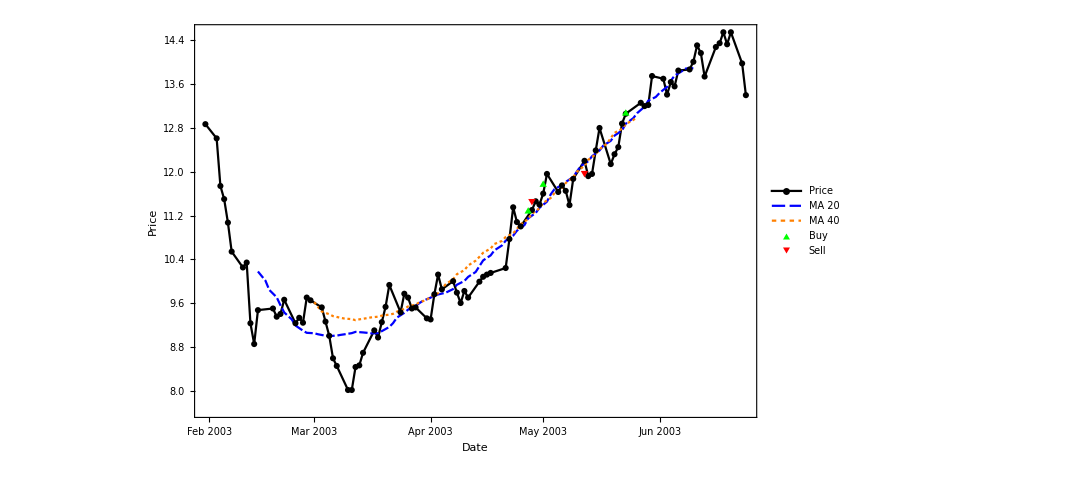

```mathematica
DateListPlot[
{MapAt[DateObject,datos,{All,1}],ma1,ma2,strategyResults["BuySignals"],strategyResults["SellSignals"]},
Joined->{True,True,True,False,False},
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize],Style["Price",bigFontSize]},
PlotLegends->{"Price","MA 20","MA 40","Buy","Sell"},
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{Black,{Thick,Blue},{Thick,Orange},Green,Red},
PlotMarkers->{Automatic,None,None,Automatic,Automatic},
ImageSize->800
]
```

### Prueba de estrategia SMA en componentes del S&P 500.

```mathematica
SaveKernelState[path_:FileNameJoin[{NotebookDirectory[],StringJoin[FileBaseName[NotebookFileName[]],"_state.mx"]}]]:=DumpSave[path,"Global`"];
LoadKernelState[path_:FileNameJoin[{NotebookDirectory[],StringJoin[FileBaseName[NotebookFileName[]],"_state.mx"]}]]:=Get[path];
```

```mathematica
CrossoverSMAReturns[marketIndex_,maWindow1_,maWindow2_]:=CrossoverTrading[
database[[marketIndex]]["DatedPrices"],
MovingAverage[#,maWindow1]&,
MovingAverage[#,maWindow2]&
]["Return"];
TradeInMarket[maWindow1_,maWindow2_]:=Module[{i},ProgressParallelTable[CrossoverSMAReturns[i,maWindow1,maWindow2],{i,1,Length[database]}]];
ProbabilityOfPositive[data_]:=Module[{x},Probability[x>0,x\[Distributed]EmpiricalDistribution[data]]];
```

```mathematica
tradingResults = Table[{w1,w2,TradeInMarket[w1,w2]},{w1,10,200,10},{w2,w1+10,200,10}];
```

```mathematica
SaveKernelState[]
```

{Global`}

Probabilidad de retorno positivo

```mathematica
probabilityOfEarning = Map[MapAt[ProbabilityOfPositive,#,{All,3}]&,DeleteCases[tradingResults,{}]];
```

```mathematica
sparseArray = Flatten[Map[{#[[1]],#[[2]]}/10->#[[3]]&,probabilityOfEarning,{2}],1];
```

```mathematica
array = SparseArray[Select[sparseArray,Last[#]>0.5&]];
```

```mathematica
MatrixPlot[array,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
PlotLabel->Style["Probabilidad de retorno positivo",bigFontSize,Black],
PlotTheme->"Monochrome",
FrameLabel->{Style["W1 (%10)",bigFontSize],Style["W2 (%10)",bigFontSize]}
]
```

-Graphics-

Media

```mathematica
returnMean = Map[MapAt[Mean,#,{All,3}]&,DeleteCases[tradingResults,{}]];
```

```mathematica
meanSparseArray = Flatten[Map[{#[[1]],#[[2]]}/10->#[[3]]&,returnMean,{2}],1];
```

```mathematica
meanArray = SparseArray[meanSparseArray];
```

```mathematica
MatrixPlot[meanArray,
ColorFunction->"Rainbow",
PlotLegends->Automatic,
PlotLabel->Style["Media de los retornos",bigFontSize,Black],
PlotTheme->"Monochrome",
FrameLabel->{Style["W1 (%10)",bigFontSize],Style["W2 (%10)",bigFontSize]}
]
```

-Graphics-